```mathematica
SetDirectory[NotebookDirectory[]];
```

# case 1: , for all

y-intercept = -3.93165 +/- 1.62777

slope = 2.01416 +/- 0.309315

correlation = -0.961519

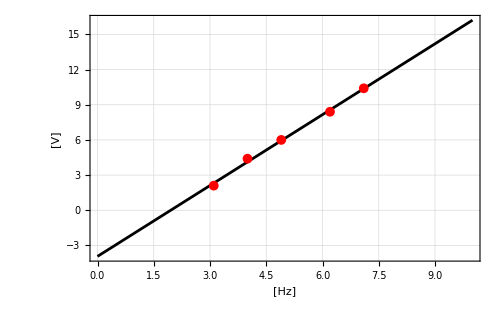

```mathematica
(*data*)
f={3.1,4.0,4.9,6.2,7.1};
Vs={2.1,4.4,6.0,8.4,10.4};
(*number of points*)
n=Length[f];
(*model*)
model[f_]:=b0+b1  f;
(*chi-square function*)
chisq=Sum[(Vs[[i]]-model[f[[i]]])^2,{i,n}];
(*best-fit values for b0 and b1*)
bestFit=Solve[{D[chisq,b0]==0,D[chisq,b1]==0},{b0,b1}]//Flatten;
(*Fisher info matrix*)
hessian=1/2 {{D[chisq,b0,b0],D[chisq,b0,b1]},{D[chisq,b0,b1],D[chisq,b1,b1]}}/. bestFit;
(*diagnostics*)
uncertainties=Sqrt[Diagonal[Inverse[hessian]]];
correlation=Inverse[hessian][[1,2]]/uncertainties[[1]]/uncertainties[[2]];
(*print results*)
Print["y-intercept = ",b0/. bestFit," +/- ",uncertainties[[1]]]
Print["slope = ",b1/. bestFit," +/- ",uncertainties[[2]]]
Print["correlation = ",correlation]
(*plot*)
Show[
Plot[
model[ff]/. bestFit,
{ff,0,10},
Frame->True,
FrameStyle->ConstantArray[{Black,Thick},4],
FrameLabel->{" [Hz]"," [V]"},
BaseStyle->{FontSize->20,FontColor->Black,FontFamily->"Latin Modern Roman"},
ImageSize->500,
PlotStyle->Black,
GridLines->Automatic,
GridLinesStyle->Black
],
ListPlot[
Transpose[{f,Vs}],
PlotStyle->Red,
PlotMarkers->{Automatic,Medium}]
]
Export["./plot.pdf",%];
```

# case 2: , for all

y-intercept = -3.85697 +/- 0.780734

slope = 2.00722 +/- 0.154176

correlation = -0.964117

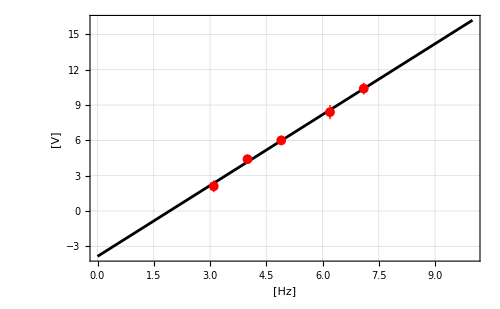

```mathematica
(*data*)
f={3.1,4.0,4.9,6.2,7.1};
Vs={2.1,4.4,6.0,8.4,10.4};
dVs={0.5,0.4,0.4,0.6,0.5};
(*number of points*)
n=Length[f];
(*model*)
model[f_]:=b0+b1  f;
(*chi-square function*)
chisq=Sum[(Vs[[i]]-model[f[[i]]])^2/dVs[[i]]^2,{i,n}];
(*best-fit values for b0 and b1*)
bestFit=Solve[{D[chisq,b0]==0,D[chisq,b1]==0},{b0,b1}]//Flatten;
(*Fisher info matrix*)
hessian=1/2 {{D[chisq,b0,b0],D[chisq,b0,b1]},{D[chisq,b0,b1],D[chisq,b1,b1]}}/. bestFit;
(*diagnostics*)
uncertainties=Sqrt[Diagonal[Inverse[hessian]]];
correlation=Inverse[hessian][[1,2]]/uncertainties[[1]]/uncertainties[[2]];
(*print results*)
Print["y-intercept = ",b0/. bestFit," +/- ",uncertainties[[1]]]
Print["slope = ",b1/. bestFit," +/- ",uncertainties[[2]]]
Print["correlation = ",correlation]
(*plot*)
Show[
Plot[
model[ff]/. bestFit,
{ff,0,10},
Frame->True,
FrameStyle->ConstantArray[{Black,Thick},4],
FrameLabel->{" [Hz]"," [V]"},
BaseStyle->{FontSize->20,FontColor->Black,FontFamily->"Latin Modern Roman"},
ImageSize->500,
PlotStyle->Black,
GridLines->Automatic,
GridLinesStyle->Black
],
ListPlot[
Transpose[{f,Table[Around[Vs[[i]],dVs[[i]]],{i,n}]}],
PlotStyle->Red,
PlotMarkers->{Automatic,Medium}]
]
(*Export["./plot.pdf",%];*)
```

# case 3: , for all

y-intercept = -4.33441 +/- 0.524907

slope = 2.10011 +/- 0.119775

correlation = -0.967084

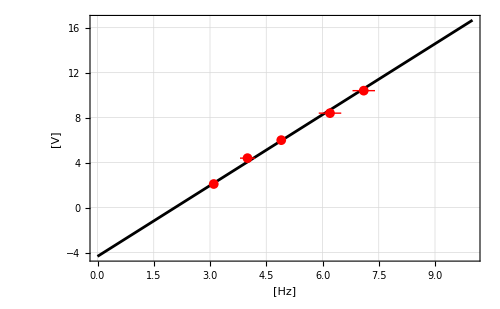

```mathematica
(*data*)
f={3.1,4.0,4.9,6.2,7.1};
df={0.1,0.2,0.1,0.3,0.3};
Vs={2.1,4.4,6.0,8.4,10.4};
(*number of points*)
n=Length[f];
(*model*)
cmodel[v_]:=c0+c1 v;
model[f_]:=b0+b1  f;
(*chi-square function*)
chisq=Sum[(f[[i]]-cmodel[Vs[[i]]])^2/df[[i]]^2,{i,n}];
(*best-fit values for b0 and b1*)
cbestFit=Solve[{D[chisq,c0]==0,D[chisq,c1]==0},{c0,c1}]//Flatten;
(*Fisher info matrix*)
chessian=1/2 {{D[chisq,c0,c0],D[chisq,c0,c1]},{D[chisq,c0,c1],D[chisq,c1,c1]}}/. cbestFit;
(*diagnostics*)
cuncertainties=Sqrt[Diagonal[Inverse[chessian]]];
ccorrelation=Inverse[chessian][[1,2]]/cuncertainties[[1]]/cuncertainties[[2]];
(*transform from cs to bs*)
bestFit={b0->-c0/c1,b1->1/c1}/. cbestFit;
J={{-1/c1,c0/c1^2},{0,-1/c1^2}}/. cbestFit;
cov=J.Inverse[chessian].Transpose[J];
uncertainties=Sqrt[Diagonal[cov]];
correlation=cov[[1,2]]/uncertainties[[1]]/uncertainties[[2]];
(*print results*)
Print["y-intercept = ",b0/. bestFit," +/- ",uncertainties[[1]]]
Print["slope = ",b1/. bestFit," +/- ",uncertainties[[2]]]
Print["correlation = ",correlation]
(*plot*)
Show[
Plot[
model[ff]/. bestFit,
{ff,0,10},
Frame->True,
FrameStyle->ConstantArray[{Black,Thick},4],
FrameLabel->{" [Hz]"," [V]"},
BaseStyle->{FontSize->20,FontColor->Black,FontFamily->"Latin Modern Roman"},
ImageSize->500,
PlotStyle->Black,
GridLines->Automatic,
GridLinesStyle->Black
],
ListPlot[
Transpose[{Table[Around[f[[i]],df[[i]]],{i,n}],Vs}],
PlotStyle->Red,
PlotMarkers->{Automatic,Medium}]
]
(*Export["./plot.pdf",%];*)
```

# case 4: , for all

y-intercept = -4.02244 +/- 1.03016

slope = 2.03759 +/- 0.213709

correlation = -0.966788

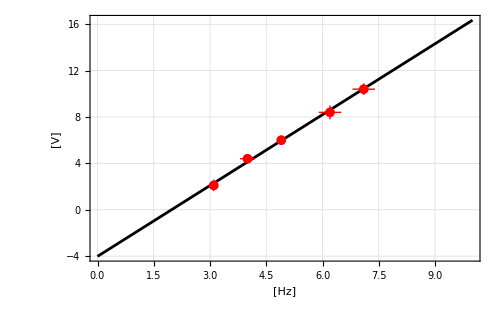

```mathematica
(*data*)
f={3.1,4.0,4.9,6.2,7.1};
df={0.1,0.2,0.1,0.3,0.3};
Vs={2.1,4.4,6.0,8.4,10.4};
dVs={0.5,0.4,0.4,0.6,0.5};
(*number of points*)
n=Length[f];
(*model*)
model[f_]:=b0+b1 f;
(*chi-square function*)
chisq=Sum[Df[i]^2/df[[i]]^2+DVs[i]^2/dVs[[i]]^2,{i,n}]/. DVs[i_]:>model[f[[i]]+Df[i]]-Vs[[i]];
(*best-fit values for c0 and c1*)
fits=NSolve[D[chisq,#]&/@Flatten[{b0,b1,Df/@Range[5]}]==0,Reals];
bestFit=MinimalBy[fits,chisq/. #&][[1]];
(*Fisher info matrix*)
params={b0,b1,Df/@Range[5]}//Flatten;
hessian=1/2 Array[D[chisq,params[[#1]],params[[#2]]]&,{Length[params],Length[params]}]/. bestFit;
(*diagnostics*)
uncertainties=Sqrt[Diagonal[Inverse[hessian]]];
correlation=Inverse[hessian][[1,2]]/uncertainties[[1]]/uncertainties[[2]];
(*print results*)
Print["y-intercept = ",b0/. bestFit," +/- ",uncertainties[[1]]]
Print["slope = ",b1/. bestFit," +/- ",uncertainties[[2]]]
Print["correlation = ",correlation]
(*plot*)
Show[
Plot[
model[ff]/. bestFit,
{ff,0,10},
Frame->True,
FrameStyle->ConstantArray[{Black,Thick},4],
FrameLabel->{" [Hz]"," [V]"},
BaseStyle->{FontSize->20,FontColor->Black,FontFamily->"Latin Modern Roman"},
ImageSize->500,
PlotStyle->Black,
GridLines->Automatic,
GridLinesStyle->Black
],
ListPlot[
Transpose[{Table[Around[f[[i]],df[[i]]],{i,n}],Table[Around[Vs[[i]],dVs[[i]]],{i,n}]}],
PlotStyle->Red,
PlotMarkers->{Automatic,Medium}]
]
(*Export["./plot.pdf",%];*)
```